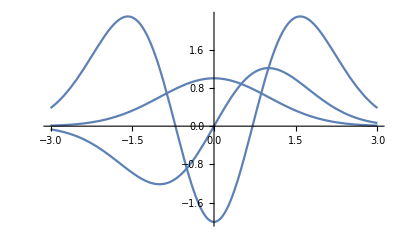

```mathematica
Clear["Global`*"]
sub={m->1,ℏ->1,ωtr->1};
xp=√((m ωtr)/ℏ)x/.sub;
Plot[Exp[-xp^2/2]HermiteH[#,xp]&/@Range[0,2,1],{x,-3,3}]
```

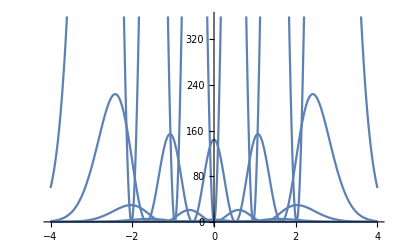

```mathematica
fts=FourierTransform[Exp[-xp^2/2]HermiteH[#,xp],x,k]&/@Range[0,5,1];
Plot[Abs[fts]^2,{k,-4,4}]
```

```mathematica
ω=(ℏ k^2)/(2m);
twfns=Assuming[t ∈ Reals, Integrate[# Exp[I k x - I ω t]/.sub,{k,-Infinity,Infinity}]&/@fts]
```

{(ⅇ^((ⅈ x^2)/(2 (-ⅈ+t))) √(2 π))/(√(1+ⅈ t)),-(2 ⅇ^((ⅈ x^2)/(2 (-ⅈ+t))) √(2 π) x)/(1+ⅈ t)^(3/2),(2 ⅇ^((ⅈ x^2)/(2 (-ⅈ+t))) √(2 π) (1+t^2-2 x^2))/(√(1+ⅈ t) (-ⅈ+t)^2),(4 ⅇ^((ⅈ x^2)/(2 (-ⅈ+t))) √(2 π) x (3+3 t^2-2 x^2))/(1+ⅈ t)^(7/2),(4 ⅇ^((ⅈ x^2)/(2 (-ⅈ+t))) √(2 π) (3 (1+t^2)^2-12 (1+t^2) x^2+4 x^4))/(√(1+ⅈ t) (-ⅈ+t)^4),-(8 ⅇ^((ⅈ x^2)/(2 (-ⅈ+t))) √(2 π) x (15 (1+t^2)^2-20 (1+t^2) x^2+4 x^4))/(1+ⅈ t)^(11/2)}

```mathematica
Manipulate[Plot[Abs[(ⅇ^((ⅈ x^2)/(2 (-ⅈ+t))) √(2 π))/(√(1+ⅈ t))]^2,{x,-10,10},PlotRange->{All,{0,7}}],{t,0,10}]
```

```mathematica
twfns[[1]]
```

(ⅇ^((ⅈ x^2)/(2 (-ⅈ+t))) √(2 π))/(√(1+ⅈ t))

```mathematica
FourierTransform[Exp[I (k+b)^2],k,x]
```

(1/2+ⅈ/2) ⅇ^(-1/4 ⅈ x (4 b+x))

```mathematica
√(1+ⅈ t) (-ⅈ+t)^2
```

```mathematica
Simplify[(1+ⅈ t)^(5/2)+√(1+ⅈ t) (-ⅈ+t)^2]
```

0